```mathematica
Hmb[a_?NumberQ,μ0_?NumberQ,Δ0_?NumberQ,V0_?NumberQ,α0_?NumberQ,dim_?IntegerQ]:=Block[{t=25/a^2,μ=μ0,α=α0/(2a),Vz=V0,Δ11=Δ0,Δ12=Δ0,H11,H12,H22,ϵ=1},H11=KroneckerProduct[PauliMatrix[3],KroneckerProduct[PauliMatrix[0],-t*(SparseArray[{Band[{1,2}]->1,Band[{2,1}]->1},{dim,dim}])+(-μ+2*t)IdentityMatrix[dim,SparseArray]]+KroneckerProduct[PauliMatrix[2],I*α*(SparseArray[{Band[{1,2}]->-1,Band[{2,1}]->1},{dim,dim}])]]+KroneckerProduct[PauliMatrix[0],KroneckerProduct[PauliMatrix[3],Vz*IdentityMatrix[dim,SparseArray]]]+KroneckerProduct[PauliMatrix[1],KroneckerProduct[PauliMatrix[0],Δ11*IdentityMatrix[dim,SparseArray]]];H22=KroneckerProduct[PauliMatrix[3],KroneckerProduct[PauliMatrix[0],-t*(SparseArray[{Band[{1,2}]->1,Band[{2,1}]->1},{dim,dim}])+(ϵ-μ+2*t)IdentityMatrix[dim,SparseArray]]+KroneckerProduct[PauliMatrix[2],I*α*(SparseArray[{Band[{1,2}]->-1,Band[{2,1}]->1},{dim,dim}])]]+KroneckerProduct[PauliMatrix[0],KroneckerProduct[PauliMatrix[3],Vz*IdentityMatrix[dim,SparseArray]]]+KroneckerProduct[PauliMatrix[1],KroneckerProduct[PauliMatrix[0],Δ11*IdentityMatrix[dim,SparseArray]]];H12=KroneckerProduct[PauliMatrix[1],KroneckerProduct[PauliMatrix[0],Δ12*IdentityMatrix[dim,SparseArray]]];Chop@ArrayFlatten[{{H11,H12},{H12,H22}}]]
```

```mathematica
Hmb[1,.2,.2,.1,5,2]//MatrixForm
```

(49.9 | -25. | 0 | -2.5 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0
-25. | 49.9 | 2.5 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0
0 | 2.5 | 49.7 | -25. | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0
-2.5 | 0 | -25. | 49.7 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2
0.2 | 0 | 0 | 0 | -49.7 | 25. | 0 | 2.5 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.2 | 0 | 0 | 25. | -49.7 | -2.5 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.2 | 0 | 0 | -2.5 | -49.9 | 25. | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.2 | 2.5 | 0 | 25. | -49.9 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 50.9 | -25. | 0 | -2.5 | 0.2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | -25. | 50.9 | 2.5 | 0 | 0 | 0.2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 2.5 | 50.7 | -25. | 0 | 0 | 0.2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | -2.5 | 0 | -25. | 50.7 | 0 | 0 | 0 | 0.2
0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 0 | -50.7 | 25. | 0 | 2.5
0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | 25. | -50.7 | -2.5 | 0
0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 0 | 0 | -2.5 | -50.9 | 25.
0 | 0 | 0 | 0.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.2 | 2.5 | 0 | 25. | -50.9)

```mathematica
Eigenvalues[Hmb[1,.2,.2,.1,5,3000],-20,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞}]
```

{0.125622,-0.125622,0.125479,-0.125479,0.125369,-0.125369,0.125287,-0.125287,0.125226,-0.125226,0.125183,-0.125183,0.125154,-0.125154,0.125134,-0.125134,0.125122,-0.125122,0.125116,-0.125116}

```mathematica
Normal@Hmb[1,.2,.2,.1,5,2]
```

{{49.9,-25.,0,-2.5,0.2,0,0,0,0,0,0,0,0.2,0,0,0},{-25.,49.9,2.5,0,0,0.2,0,0,0,0,0,0,0,0.2,0,0},{0,2.5,49.7,-25.,0,0,0.2,0,0,0,0,0,0,0,0.2,0},{-2.5,0,-25.,49.7,0,0,0,0.2,0,0,0,0,0,0,0,0.2},{0.2,0,0,0,-49.7,25.,0,2.5,0.2,0,0,0,0,0,0,0},{0,0.2,0,0,25.,-49.7,-2.5,0,0,0.2,0,0,0,0,0,0},{0,0,0.2,0,0,-2.5,-49.9,25.,0,0,0.2,0,0,0,0,0},{0,0,0,0.2,2.5,0,25.,-49.9,0,0,0,0.2,0,0,0,0},{0,0,0,0,0.2,0,0,0,50.9,-25.,0,-2.5,0.2,0,0,0},{0,0,0,0,0,0.2,0,0,-25.,50.9,2.5,0,0,0.2,0,0},{0,0,0,0,0,0,0.2,0,0,2.5,50.7,-25.,0,0,0.2,0},{0,0,0,0,0,0,0,0.2,-2.5,0,-25.,50.7,0,0,0,0.2},{0.2,0,0,0,0,0,0,0,0.2,0,0,0,-50.7,25.,0,2.5},{0,0.2,0,0,0,0,0,0,0,0.2,0,0,25.,-50.7,-2.5,0},{0,0,0.2,0,0,0,0,0,0,0,0.2,0,0,-2.5,-50.9,25.},{0,0,0,0.2,0,0,0,0,0,0,0,0.2,2.5,0,25.,-50.9}}

```mathematica
data=Block[{vzm=1,vzstep=0.02,μ=0.1,α=2,Δ=0.2},ParallelTable[First@Sort[Select[Re@Eigenvalues[Hmb[1,μ,Δ,vz,α,3000],-20,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞}],#>0&]],{vz,0,vzm,vzstep}]]
```

$Aborted

```mathematica
data=Block[{vzm=1,vzstep=0.02,μ=0.1,α=2,Δ=0.2},ParallelTable[{vz,Min@Abs@Eigenvalues[Hmb[1,μ,Δ,vz,α,3000],-20,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞}]},{vz,0,vzm,vzstep}]]
```

{{0.,0.183305},{0.02,0.168786},{0.04,0.148913},{0.06,0.128916},{0.08,0.108918},{0.1,0.088922},{0.12,0.0689275},{0.14,0.0489371},{0.16,0.0289591},{0.18,0.00906687},{0.2,1.46765×10^-10},{0.22,3.24556×10^-18},{0.24,2.22027×10^-15},{0.26,8.06606×10^-16},{0.28,5.15333×10^-16},{0.3,9.37392×10^-16},{0.32,6.20041×10^-17},{0.34,1.68691×10^-15},{0.36,2.57346×10^-15},{0.38,1.08775×10^-15},{0.4,6.74942×10^-16},{0.42,1.40315×10^-15},{0.44,1.09174×10^-15},{0.46,2.20354×10^-15},{0.48,1.49365×10^-15},{0.5,1.24246×10^-15},{0.52,2.28161×10^-16},{0.54,8.53456×10^-17},{0.56,8.35001×10^-17},{0.58,1.44592×10^-16},{0.6,4.84901×10^-17},{0.62,2.59744×10^-17},{0.64,1.32033×10^-15},{0.66,1.0514×10^-16},{0.68,3.51146×10^-16},{0.7,4.13521×10^-16},{0.72,7.45994×10^-16},{0.74,1.12041×10^-15},{0.76,7.75079×10^-15},{0.78,1.74471×10^-14},{0.8,3.71297×10^-14},{0.82,7.49228×10^-14},{0.84,1.52402×10^-13},{0.86,2.85739×10^-13},{0.88,5.01973×10^-13},{0.9,7.98483×10^-13},{0.92,1.04111×10^-12},{0.94,8.40225×10^-13},{0.96,5.97857×10^-13},{0.98,8.20776×10^-16},{1.,3.33277×10^-15}}

```mathematica
data2=Block[{vzm=1,vzstep=0.01,μ=0.1,α=2,Δ=0.2},ParallelTable[First@Sort[Select[Re@Eigenvalues[SparseArray@Hc[1,μ,Δ,vz,α,3000],-10,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->∞}],#>0&]],{vz,0,vzm,vzstep}]]
```

```mathematica
Dynamic[vz]
```

```mathematica
data//Length
```

51

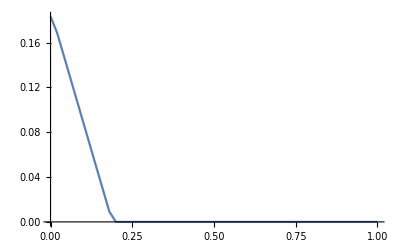

```mathematica
ListLinePlot[data,PlotRange->Full]
```

```mathematica
store=Import["D:\\Nanowire\\fitexpSA\\multiband_matlab\\store.dat"]
```

{{0.183476,0.168213,0.147809,0.127403,0.106998,0.0865942,0.0661923,0.0457957,0.0254166,0.00522156,1.13113×10^-13,1.49029×10^-16,5.79195×10^-16,2.70159×10^-16,1.53194×10^-15,1.35534×10^-16,3.9376×10^-17,2.84461×10^-16,2.61782×10^-16,9.65709×10^-17,8.38813×10^-17,2.30923×10^-17,1.71286×10^-16,6.98057×10^-17,4.19785×10^-16,2.70183×10^-16,2.34491×10^-17,6.47868×10^-16,2.81564×10^-16,4.0532×10^-16,4.95099×10^-16,9.82811×10^-17,1.57179×10^-15,1.24014×10^-16,1.38666×10^-17,4.50427×10^-16,5.65232×10^-16,4.05233×10^-15,7.72598×10^-15,5.29696×10^-15,1.7873×10^-14,7.64678×10^-14,1.86335×10^-13,3.54162×10^-13,5.9207×10^-13,9.24557×10^-13,1.42655×10^-12,2.26916×10^-12,3.82889×10^-12,6.79984×10^-12},{0.183305,0.168391,0.148097,0.127691,0.107286,0.0868817,0.0664794,0.0460819,0.0257005,0.00548285,2.31447×10^-13,5.12103×10^-16,8.13325×10^-16,2.78791×10^-15,4.54607×10^-16,1.15673×10^-16,1.58201×10^-16,3.4222×10^-16,3.19218×10^-17,2.79929×10^-16,2.32291×10^-16,3.62155×10^-16,6.88213×10^-17,4.61554×10^-16,2.04614×10^-15,1.11733×10^-15,3.18742×10^-16,3.48786×10^-16,4.48898×10^-17,3.00636×10^-16,1.94595×10^-15,6.32172×10^-16,2.14503×10^-16,2.21034×10^-17,8.04877×10^-17,7.72794×10^-16,1.6962×10^-15,1.61878×10^-15,2.06907×10^-15,1.17178×10^-14,3.36741×10^-14,7.57286×10^-14,1.46302×10^-13,2.46516×10^-13,3.42949×10^-13,3.14174×10^-13,1.43656×10^-13,1.62551×10^-12,1.63362×10^-15,6.70047×10^-15},{0.183313,0.177623,0.164731,0.149127,0.132495,0.115401,0.0980041,0.0802176,0.0616079,0.0414487,0.0210642,0.00115811,2.09312×10^-16,1.84142×10^-16,3.02831×10^-16,1.27986×10^-16,7.52541×10^-17,6.86971×10^-17,2.33583×10^-16,2.67919×10^-16,1.22732×10^-18,3.10419×10^-16,2.04327×10^-16,4.02361×10^-16,1.26718×10^-16,3.57982×10^-16,1.1207×10^-16,5.37125×10^-17,4.34182×10^-16,2.22851×10^-15,1.98947×10^-16,1.39854×10^-16,2.82378×10^-16,5.56992×10^-17,1.28584×10^-16,1.11101×10^-15,2.54995×10^-15,6.27717×10^-15,1.71888×10^-14,4.18392×10^-14,9.50978×10^-14,1.90528×10^-13,3.19204×10^-13,4.15174×10^-13,1.65746×10^-15,5.10018×10^-15,5.45569×10^-15,9.02502×10^-15,2.16745×10^-14,1.64719×10^-13},{0.183304,0.180078,0.171611,0.160039,0.146883,0.132982,0.118782,0.104522,0.0903114,0.0761575,0.0619284,0.047213,0.0306903,0.0105223,1.69406×10^-13,2.70019×10^-16,4.99097×10^-18,1.85519×10^-15,6.5513×10^-16,1.61947×10^-16,2.31755×10^-16,2.57424×10^-16,4.94592×10^-16,8.26695×10^-17,1.49247×10^-17,6.59435×10^-17,2.26326×10^-16,2.95654×10^-17,9.26569×10^-16,1.55281×10^-16,1.2113×10^-16,6.41862×10^-16,2.85118×10^-16,3.68961×10^-16,8.70348×10^-16,2.6516×10^-15,4.12071×10^-15,1.70247×10^-15,1.44246×10^-14,5.9634×10^-14,1.34294×10^-13,2.38053×10^-16,6.9708×10^-15,3.21148×10^-15,4.11854×10^-15,1.03342×10^-14,2.36073×10^-13,3.00874×10^-14,4.18274×10^-14,2.29128×10^-13},{0.183325,0.181057,0.174858,0.165842,0.155084,0.143349,0.13113,0.118738,0.106366,0.0941276,0.0820705,0.0701688,0.0582888,0.0460757,0.0325112,0.0140666,7.64844×10^-12,9.77431×10^-17,2.10271×10^-16,1.02314×10^-16,4.79582×10^-16,2.35285×10^-16,1.77107×10^-15,2.58899×10^-16,7.22515×10^-16,7.35879×10^-17,3.0748×10^-16,1.71904×10^-16,1.61603×10^-15,9.53634×10^-17,1.86098×10^-16,7.52022×10^-17,1.40812×10^-17,2.54139×10^-15,2.05661×10^-15,4.23464×10^-15,1.36641×10^-15,1.54045×10^-14,2.80083×10^-17,1.71662×10^-17,3.11885×10^-15,1.81867×10^-15,4.07887×10^-15,3.90046×10^-14,1.06023×10^-14,2.26514×10^-14,9.70296×10^-14,4.55053×10^-14,1.46347×10^-13,1.61712×10^-13},{0.183303,0.181557,0.17665,0.169262,0.160162,0.149981,0.139177,0.128068,0.116869,0.10572,0.0947024,0.0838394,0.0730783,0.062222,0.0505935,0.0323995,0.0120065,9.54864×10^-16,1.38293×10^-16,2.25478×10^-16,2.04495×10^-15,2.1945×10^-16,2.26598×10^-16,1.82308×10^-16,7.74588×10^-16,3.36521×10^-16,1.23515×10^-16,1.13362×10^-16,2.07953×10^-16,3.07798×10^-16,5.54481×10^-17,2.0012×10^-16,3.23374×10^-16,1.48166×10^-15,1.04343×10^-15,4.29464×10^-15,1.49886×10^-14,8.52931×10^-16,5.90572×10^-16,1.13107×10^-15,1.25755×10^-14,3.33904×10^-15,1.23081×10^-14,1.67913×10^-14,2.1131×10^-14,1.1343×10^-13,4.7573×10^-14,4.11512×10^-13,1.17433×10^-13,3.94335×10^-13},{0.183303,0.181853,0.177748,0.171439,0.163503,0.154456,0.144704,0.134548,0.124203,0.113815,0.103475,0.0932178,0.0752889,0.0548827,0.0344787,0.0140856,4.25424×10^-13,3.875×10^-16,6.49118×10^-17,4.28232×10^-17,5.08623×10^-17,5.52913×10^-16,1.30748×10^-16,4.66406×10^-18,2.64152×10^-16,5.79101×10^-16,6.54689×10^-16,7.3322×10^-17,5.20341×10^-16,4.89521×10^-17,1.39147×10^-16,1.56633×10^-15,3.37894×10^-16,1.54713×10^-15,4.34909×10^-15,3.39977×10^-15,1.85696×10^-14,2.03575×10^-15,1.28766×10^-15,3.95752×10^-15,4.89265×10^-15,1.25232×10^-14,1.58333×10^-14,2.80173×10^-14,4.24418×10^-14,6.52938×10^-14,1.08999×10^-13,1.54123×10^-13,2.31348×10^-13,3.70758×10^-13},{0.183303,0.182039,0.178462,0.172887,0.165775,0.157553,0.148577,0.132947,0.11254,0.0921339,0.0717279,0.0513234,0.030923,0.0105498,8.69455×10^-16,3.13618×10^-16,5.1919×10^-17,3.47607×10^-17,5.46496×10^-17,9.63182×10^-16,9.95473×10^-17,3.25895×10^-17,4.56355×10^-16,8.33272×10^-16,2.78374×10^-17,3.03844×10^-16,2.87533×10^-16,3.72092×10^-16,3.00488×10^-16,1.1343×10^-16,9.70834×10^-17,4.05971×10^-16,2.85495×10^-16,3.07709×10^-15,2.83501×10^-15,1.27117×10^-14,6.19846×10^-15,4.1811×10^-14,3.76056×10^-15,1.09199×10^-13,3.09396×10^-14,1.27011×10^-14,1.28197×10^-13,3.20134×10^-14,1.2737×10^-13,8.56757×10^-14,1.65652×10^-13,2.66856×10^-13,2.61407×10^-13,1.50773×10^-12},{0.183305,0.182166,0.178927,0.1639,0.143494,0.123089,0.102683,0.0822779,0.0618743,0.0414746,0.0210897,0.00117284,2.94166×10^-16,2.38664×10^-15,2.86259×10^-16,1.3411×10^-16,9.80613×10^-19,1.10602×10^-16,2.02031×10^-16,7.55618×10^-17,3.2442×10^-16,2.61516×10^-17,1.14154×10^-16,1.86382×10^-15,2.73525×10^-17,3.19956×10^-16,4.44007×10^-16,1.59979×10^-16,3.78741×10^-17,1.73014×10^-15,4.35055×10^-19,9.19753×10^-16,1.0976×10^-15,3.06641×10^-15,9.04568×10^-15,7.03587×10^-16,2.96984×10^-14,2.66424×10^-14,5.62956×10^-14,1.24144×10^-13,1.77296×10^-14,3.03245×10^-13,2.51272×10^-13,4.15018×10^-13,1.0516×10^-13,2.3534×10^-13,1.61653×10^-13,7.68211×10^-13,4.18279×10^-13,5.37158×10^-13},{0.183346,0.168513,0.148108,0.127703,0.107298,0.0868932,0.0664909,0.0460934,0.0257119,0.00549291,7.26522×10^-14,1.8059×10^-17,4.42126×10^-17,3.86209×10^-16,2.0564×10^-17,1.56869×10^-16,8.44859×10^-16,1.20393×10^-15,1.77437×10^-16,1.44473×10^-16,8.00459×10^-17,6.96465×10^-16,7.1471×10^-16,2.76562×10^-16,5.30766×10^-16,1.12412×10^-16,1.09296×10^-16,1.31742×10^-15,2.23124×10^-15,1.62754×10^-16,5.27995×10^-16,1.0544×10^-15,1.03862×10^-15,6.80062×10^-15,7.46166×10^-15,1.00432×10^-14,3.97923×10^-14,3.36016×10^-14,5.42449×10^-14,1.64317×10^-13,1.07755×10^-13,2.22104×10^-13,5.51244×10^-13,2.97291×10^-13,7.32436×10^-13,1.62788×10^-12,8.28994×10^-13,1.9887×10^-12,6.15622×10^-13,2.63837×10^-12},{0.183303,0.168157,0.147797,0.127392,0.106986,0.0865823,0.0661805,0.0457839,0.0254048,0.0052103,3.36465×10^-13,3.19099×10^-16,8.66733×10^-17,1.71005×10^-17,8.19925×10^-16,6.15885×10^-17,5.42158×10^-16,3.68228×10^-16,2.39133×10^-16,5.22585×10^-17,1.26919×10^-15,3.58127×10^-17,1.19602×10^-16,4.09626×10^-17,1.64107×10^-17,2.17612×10^-17,3.26915×10^-16,1.43823×10^-16,4.36005×10^-16,4.78549×10^-16,9.53833×10^-16,7.34635×10^-16,4.52176×10^-16,8.70755×10^-15,1.31023×10^-14,4.27862×10^-16,3.98745×10^-14,7.80873×10^-14,4.81614×10^-14,9.84621×10^-14,2.97697×10^-13,3.16242×10^-13,8.57364×10^-14,8.21688×10^-13,1.25764×10^-12,5.28472×10^-13,1.55525×10^-12,3.6894×10^-12,3.39094×10^-12,9.7086×10^-13},{0.183303,0.177897,0.165432,0.150181,0.133853,0.117058,0.100002,0.0826704,0.0647903,0.0454707,0.0250869,0.00484842,1.09683×10^-14,1.10127×10^-16,1.00694×10^-16,1.9349×10^-16,2.05447×10^-16,2.49048×10^-16,3.32372×10^-16,4.84079×10^-16,2.67243×10^-16,2.4473×10^-17,1.81574×10^-16,7.32463×10^-17,1.10554×10^-16,2.10895×10^-15,3.35922×10^-16,3.857×10^-17,1.29333×10^-16,7.20014×10^-16,1.86073×10^-15,2.48995×10^-15,9.93218×10^-16,6.48255×10^-15,2.09168×10^-14,3.377×10^-14,2.3035×10^-14,3.37813×10^-14,1.3681×10^-13,2.24635×10^-13,1.66729×10^-13,1.47519×10^-13,6.68347×10^-13,1.06436×10^-12,7.9467×10^-13,5.24983×10^-13,2.58751×10^-12,4.11251×10^-12,3.2328×10^-12,1.18224×10^-12},{0.18331,0.180269,0.172289,0.16131,0.148729,0.135362,0.121674,0.107942,0.0943321,0.0809378,0.0677907,0.0548381,0.0418581,0.0281154,0.0103104,2.22398×10^-12,3.40446×10^-17,4.07386×10^-17,1.55146×10^-17,3.23094×10^-16,1.99642×10^-16,1.31486×10^-16,2.84307×10^-16,2.45549×10^-16,9.82475×10^-16,2.71248×10^-16,5.5074×10^-17,3.42322×10^-17,2.65465×10^-16,2.89591×10^-16,1.15135×10^-15,4.31654×10^-15,8.95079×10^-15,1.35121×10^-14,1.14355×10^-14,6.73939×10^-15,5.11771×10^-14,1.15611×10^-13,1.67668×10^-13,1.39692×10^-13,4.52859×10^-14,4.15703×10^-13,8.7096×10^-13,1.12796×10^-12,7.78622×10^-13,4.92379×10^-13,2.59326×10^-12,4.71343×10^-12,5.3868×10^-12,3.08162×10^-12},{0.183305,0.181128,0.175253,0.166834,0.156767,0.145683,0.134045,0.122188,0.110351,0.0987083,0.0873913,0.0764978,0.0660965,0.0562216,0.0468617,0.0379363,0.0292403,0.0202515,0.0086374,3.52216×10^-16,4.05778×10^-17,5.4344×10^-17,1.07416×10^-16,7.05253×10^-17,8.57651×10^-16,1.0356×10^-16,3.90475×10^-16,4.41809×10^-16,1.03125×10^-15,1.57814×10^-15,2.08653×10^-15,4.93774×10^-15,5.15619×10^-15,9.32402×10^-16,1.24688×10^-14,4.06371×10^-14,8.49549×10^-14,1.35857×10^-13,1.65471×10^-13,1.18066×10^-13,6.5601×10^-14,4.28557×10^-13,9.3606×10^-13,1.42619×10^-12,1.58747×10^-12,1.00794×10^-12,6.59998×10^-13,3.40528×10^-12,6.75685×10^-12,9.35526×10^-12},{0.18332,0.181449,0.17657,0.169713,0.161397,0.151939,0.141744,0.131176,0.120511,0.109953,0.0996578,0.0897428,0.0802977,0.071385,0.0630405,0.0552729,0.0480635,0.041365,0.0350996,0.0291504,0.0233339,0.0173076,0.01007,1.58272×10^-11,1.9351×10^-16,6.96301×10^-17,1.2235×10^-16,2.79964×10^-16,8.31314×10^-16,2.18857×10^-16,1.94632×10^-15,1.91065×10^-15,6.04445×10^-17,6.43537×10^-15,2.35095×10^-14,5.22993×10^-14,1.0161×10^-13,1.6473×10^-13,2.2796×10^-13,2.57683×10^-13,1.95909×10^-13,3.27226×10^-14,5.01758×10^-13,1.24093×10^-12,2.18594×10^-12,3.10075×10^-12,3.58381×10^-12,3.10389×10^-12,9.31701×10^-13,3.33162×10^-12},{0.183318,0.181344,0.176607,0.170808,0.16407,0.155871,0.146791,0.137259,0.127557,0.117891,0.108416,0.0992543,0.0904956,0.0822055,0.0744261,0.0671779,0.0604618,0.054261,0.0485439,0.043266,0.0383717,0.0337951,0.0294578,0.0252627,0.021078,0.0166909,0.0116285,0.00309649,6.64471×10^-17,1.13837×10^-15,1.70353×10^-15,2.22915×10^-15,5.10933×10^-16,2.38776×10^-15,1.18338×10^-14,3.68294×10^-14,8.10728×10^-14,1.55327×10^-13,2.69362×10^-13,4.23994×10^-13,6.07974×10^-13,7.84899×10^-13,8.76673×10^-13,7.64091×10^-13,2.81239×10^-13,7.38785×10^-13,2.44175×10^-12,4.96201×10^-12,8.14526×10^-12,1.12599×10^-11},{0.183321,0.180526,0.175576,0.170683,0.165616,0.158485,0.150364,0.141744,0.132896,0.124019,0.115266,0.106755,0.0985761,0.0907954,0.0834574,0.0765877,0.0701953,0.0642745,0.058808,0.0537685,0.0491214,0.0448264,0.040839,0.0371109,0.033591,0.0302241,0.0269502,0.0237005,0.0203895,0.0168933,0.0129819,0.00798108,7.22141×10^-13,2.05607×10^-14,3.0159×10^-14,4.03136×10^-14,4.69873×10^-14,4.21908×10^-14,1.21799×10^-14,6.45414×10^-14,2.20769×10^-13,4.99239×10^-13,9.5055×10^-13,1.62663×10^-12,2.55635×10^-12,3.73161×10^-12,5.13508×10^-12,6.64288×10^-12,7.77992×10^-12,7.95589×10^-12},{0.183304,0.179718,0.175593,0.171634,0.167006,0.160571,0.153247,0.145409,0.137303,0.129115,0.120992,0.113049,0.105374,0.0980326,0.0910704,0.0845166,0.0783849,0.0726766,0.0673822,0.0624835,0.0579557,0.0537689,0.0498895,0.0462814,0.0429068,0.0397275,0.0367051,0.0338025,0.0309835,0.0282139,0.02546,0.0226866,0.0198512,0.0168928,0.0137031,0.0100294,0.00481058,2.06519×10^-13,3.34564×10^-13,5.0799×10^-13,7.48027×10^-13,1.07188×10^-12,1.49359×10^-12,2.01252×10^-12,2.60694×10^-12,3.23782×10^-12,3.87715×10^-12,4.38155×10^-12,4.30621×10^-12,3.16235×10^-12},{0.183323,0.18006,0.176742,0.173295,0.168493,0.162548,0.155847,0.148652,0.141171,0.133573,0.125995,0.118545,0.111308,0.104349,0.0977137,0.0914335,0.0855251,0.0799944,0.0748371,0.0700409,0.0655874,0.0614528,0.0576101,0.0540295,0.0506798,0.0475296,0.0445479,0.0417057,0.0389762,0.0363361,0.0337656,0.0312483,0.0287701,0.0263185,0.0238807,0.0214413,0.0189786,0.0164592,0.0138254,0.0109615,0.00756475,0.00128302,9.83041×10^-13,1.32809×10^-12,1.69392×10^-12,2.06639×10^-12,2.47074×10^-12,2.89263×10^-12,3.04938×10^-12,2.31747×10^-12},{0.183314,0.18128,0.17841,0.174723,0.170038,0.164499,0.158298,0.151633,0.144678,0.137583,0.130474,0.123452,0.116598,0.109974,0.103626,0.0975854,0.0918721,0.0864946,0.0814524,0.0767375,0.0723359,0.0682285,0.0643929,0.0608042,0.0574358,0.0542611,0.0512541,0.0483907,0.045649,0.0430103,0.0404593,0.0379838,0.0355745,0.0332243,0.0309275,0.0286792,0.0264741,0.0243062,0.0221677,0.020048,0.0179321,0.0157976,0.0136096,0.0113069,0.00876337,0.0056103,1.2447×10^-12,3.49517×10^-12,4.9613×10^-12,6.74611×10^-12},{0.183408,0.182136,0.179528,0.175972,0.171553,0.166382,0.160609,0.154395,0.147891,0.141232,0.134531,0.127883,0.121365,0.115036,0.108941,0.103113,0.0975718,0.0923285,0.0873854,0.0827377,0.078375,0.074282,0.07044,0.0668281,0.063424,0.060205,0.0571494,0.0542367,0.0514488,0.0487701,0.0461878,0.043692,0.0412748,0.0389307,0.0366552,0.034445,0.0322971,0.0302086,0.0281764,0.0261968,0.0242653,0.0223763,0.0205228,0.0186961,0.0168846,0.0150724,0.0132368,0.0113422,0.00932565,0.00705067}}

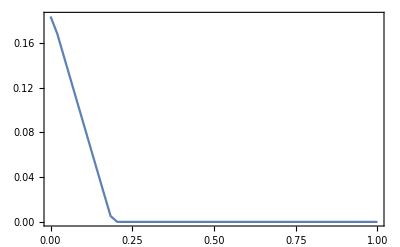
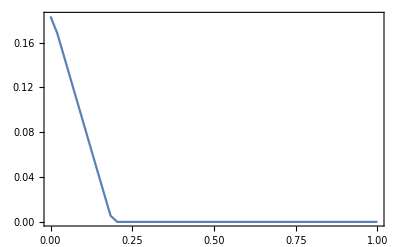
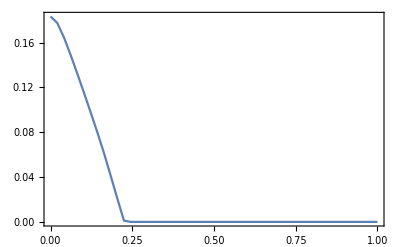
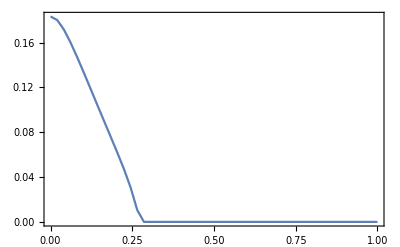
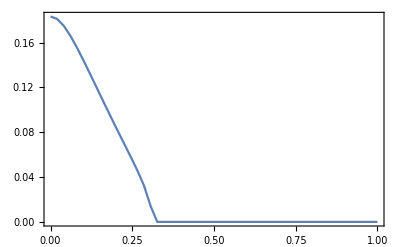
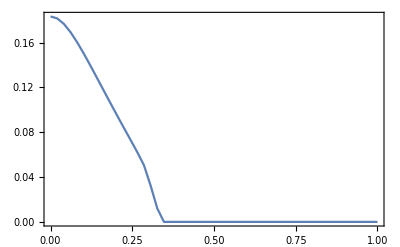
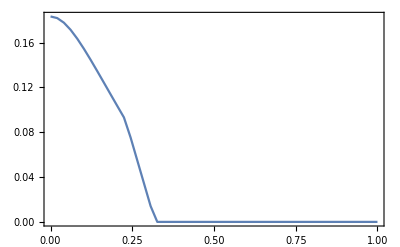
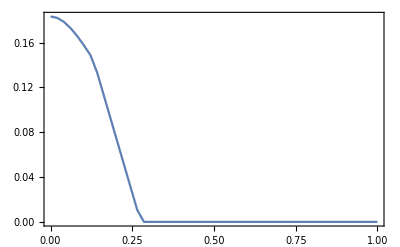

```mathematica
ListLinePlot[store[[#]],PlotRange->Full,Frame->True,DataRange->{0,1}]&/@Range[1,21]
```

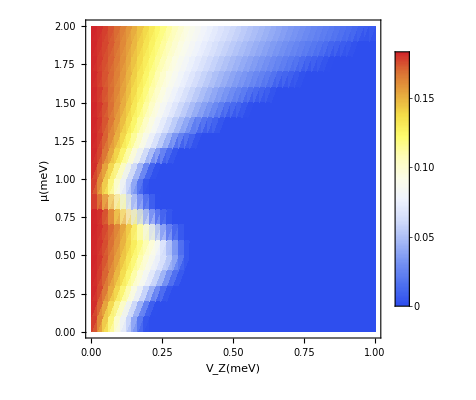

```mathematica
ListDensityPlot[store,PlotLegends->Automatic,ColorFunction->"TemperatureMap",DataRange->{{0,1},{0,2}},FrameLabel->{"V_Z(meV)","μ(meV)"}]
```

```mathematica
delta120p1=Import[NotebookDirectory[]<>"\\delta120.1.dat"];
```

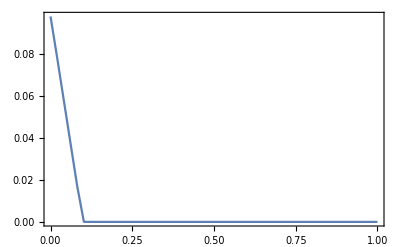
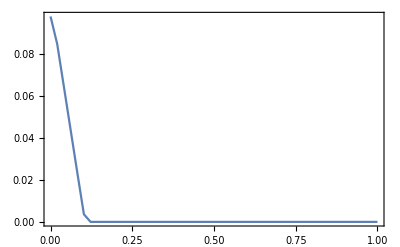
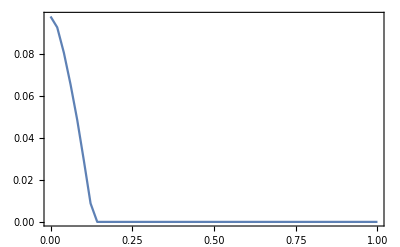
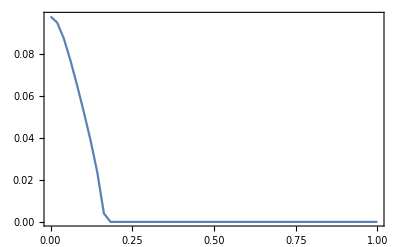
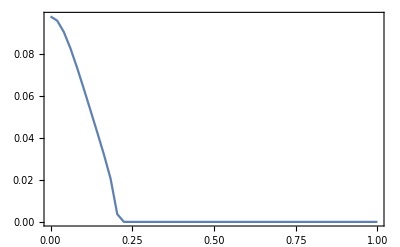
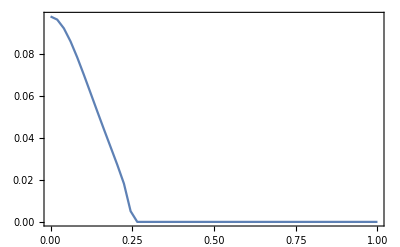
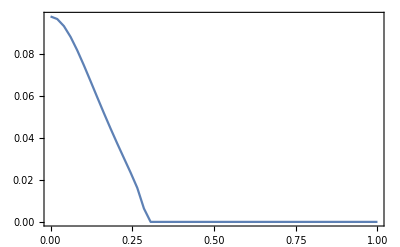
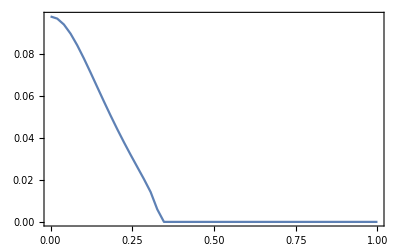

```mathematica
ListLinePlot[#,PlotRange->Full,Frame->True,DataRange->{0,1}]&/@delta120p1
```

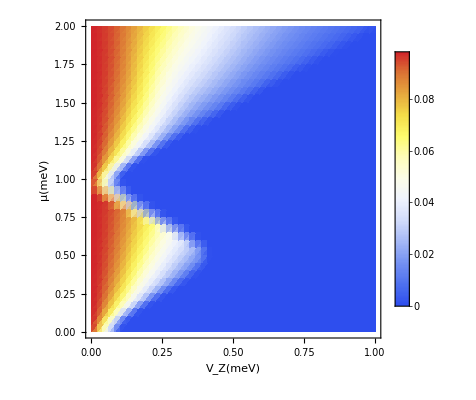

```mathematica
ListDensityPlot[delta120p1,PlotLegends->Automatic,ColorFunction->"TemperatureMap",DataRange->{{0,1},{0,2}},FrameLabel->{"V_Z(meV)","μ(meV)"}]
```

```mathematica
delta120p2=Import[NotebookDirectory[]<>"\\delta120.2.dat"];
```

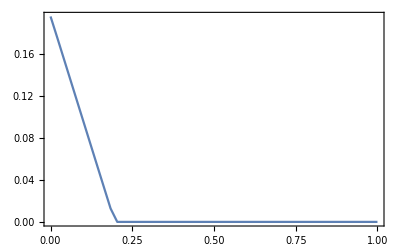
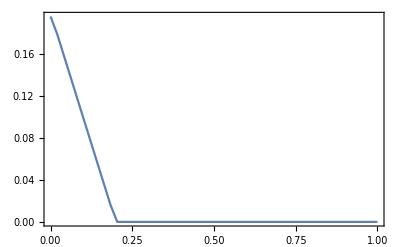
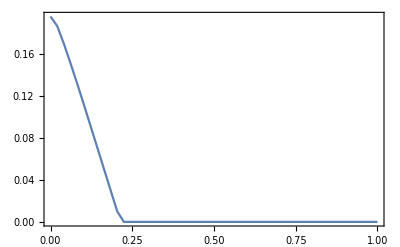
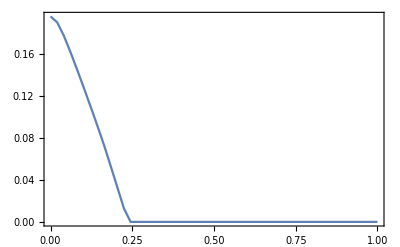
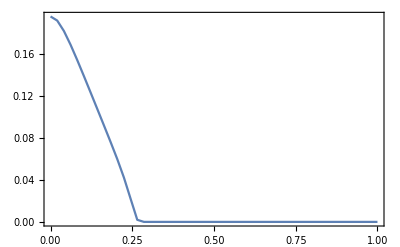
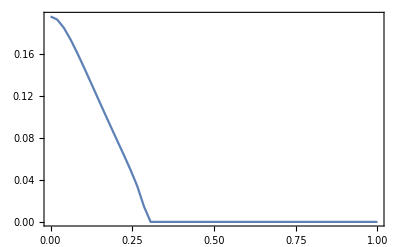
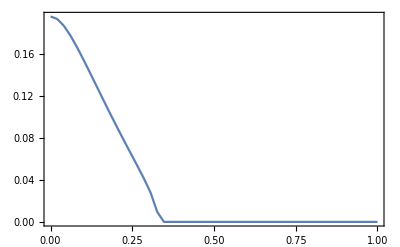
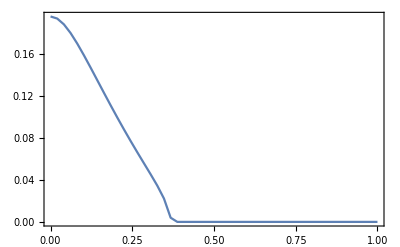

```mathematica
ListLinePlot[#,PlotRange->Full,Frame->True,DataRange->{0,1}]&/@delta120p2
```

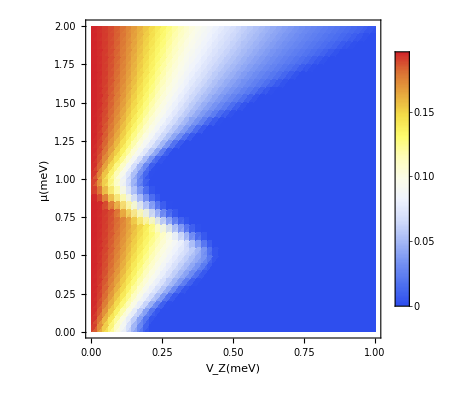

```mathematica
ListDensityPlot[delta120p2,PlotLegends->Automatic,ColorFunction->"TemperatureMap",DataRange->{{0,1},{0,2}},FrameLabel->{"V_Z(meV)","μ(meV)"}]
```

```mathematica
delta120p3=Import[NotebookDirectory[]<>"\\delta120.3.dat"];
```

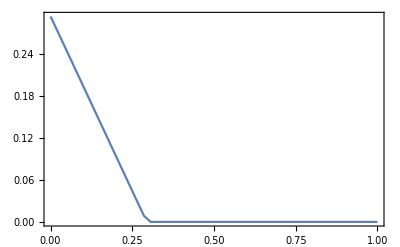
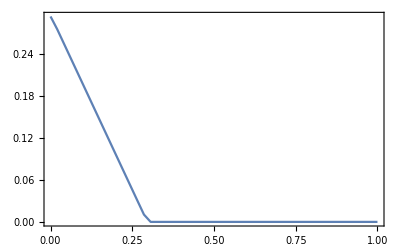
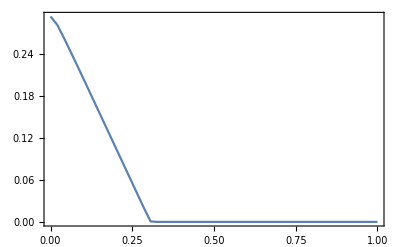
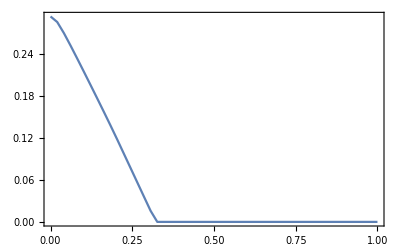
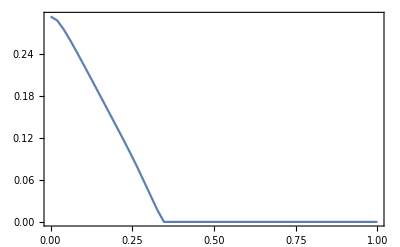
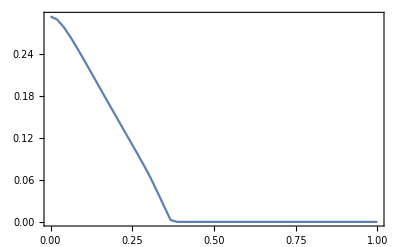
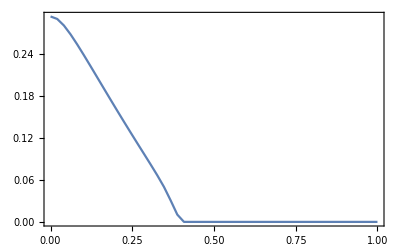
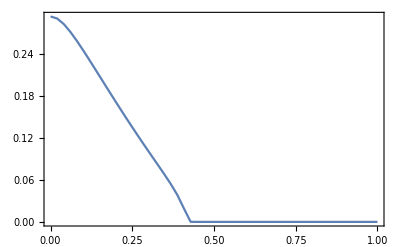
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot[#,PlotRange->Full,Frame->True,DataRange->{0,1}]&/@delta120p3
```

```mathematica
ListDensityPlot[delta120p3,PlotLegends->Automatic,ColorFunction->"TemperatureMap",DataRange->{{0,1},{0,2}},FrameLabel->{"V_Z(meV)","μ(meV)"}]
```

-Graphics-

```mathematica
delta120p4=Import[NotebookDirectory[]<>"\\delta120.4.dat"];
```

```mathematica
ListLinePlot[#,PlotRange->Full,Frame->True,DataRange->{0,1}]&/@delta120p4
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListDensityPlot[delta120p4,PlotLegends->Automatic,ColorFunction->"TemperatureMap",DataRange->{{0,1},{0,2}},FrameLabel->{"V_Z(meV)","μ(meV)"}]
```

-Graphics-